```mathematica
Exit[]
```

```mathematica
g=FinancialData["DAX","1.1.1900"];
```

```mathematica
g[[1]]
```

{{1990,11,26},1443.2}

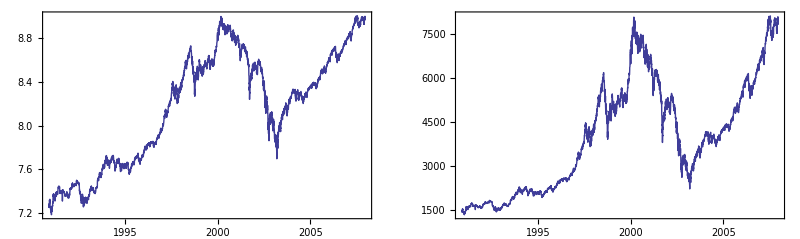

```mathematica
GraphicsRow[{DateListPlot[{{#1,Log[#2]}&@@@g},Joined->True],DateListPlot[{g},Joined->True]}]
```

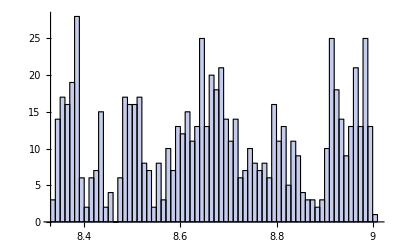

```mathematica
Histogram[Log[#2]&@@@g,HistogramCategories->50]
```

```mathematica
d=Differences[Log[10,#2]&@@@g];
```

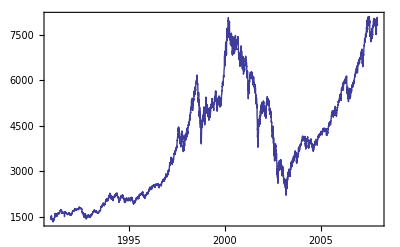

```mathematica
DateListPlot[{g},Joined->True]
```

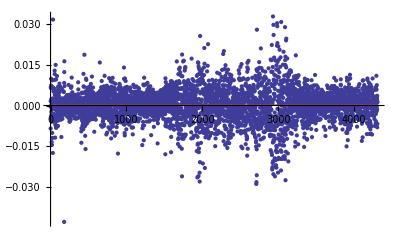

```mathematica
Show[ListPlot[d,PlotRange->All],Plot[{,Mean[d]},{x,0,Length[d]}]]
```

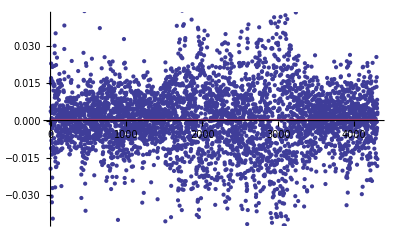

```mathematica
Show[ListPlot[10^d-1],Plot[{,10^Mean[d]-1},{x,0,Length[d]}]]
```

```mathematica
Mean[d]
Log[10,g[[Length[g],2]]/g[[1,2]]]/Length[d]
```

0.000357102

0.000357102

```mathematica
U={g[[1,2]]};
For[i=0,i<Length[d],i++,
AppendTo[U,U[[i+1]] 10^(d[[i+1]]) ];
]
```

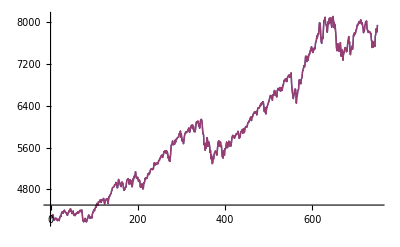

```mathematica
ListPlot[{U,#2&@@@g},Joined->True]
```

```mathematica
<<Histograms`
```

HistogramCategories::shdw: Symbol "HistogramCategories" appears in multiple contexts {"Histograms`", "Global`"}; definitions in context "Histograms`" may shadow or be shadowed by other definitions.

Histogram::shdw: Symbol "Histogram" appears in multiple contexts {"Histograms`", "Global`"}; definitions in context "Histograms`" may shadow or be shadowed by other definitions.

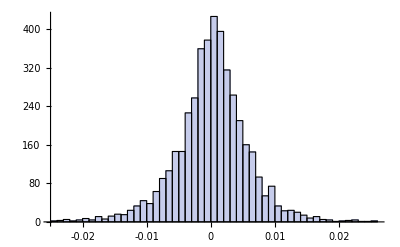

```mathematica
Histogram[d,HistogramCategories->80;HistogramRange->{-.025,.025}]
```

```mathematica
sd[i_,n_]:=If[i==1,0,StandardDeviation[d[[Max[i-n+1,1];;i]]]]
```

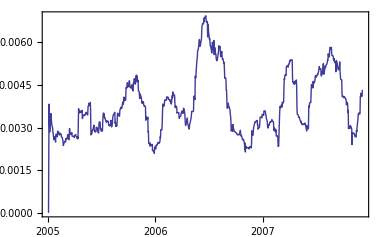

```mathematica
DateListPlot[Table[{g[[i,1]],sd[i,30] },{i,1,Length[d]}],Joined->True]
```

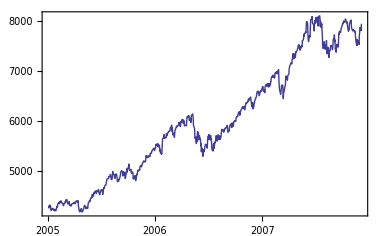

```mathematica
DateListPlot[{g},Joined->True]
```

```mathematica
vd=FinancialData["V1X","1.1.2005"];
```

FinancialData::notent: "V1X" is not a known entity in FinancialData.

```mathematica
g
```

{{{2005,2,24},0.22},{{2005,6,23},0.22},{{2005,9,22},0.22},{{2005,12,22},0.25},{{2006,2,23},0.25},{{2006,6,22},0.25},{{2006,9,21},0.25},{{2006,12,21},0.28},{{2007,2,22},0.28},{{2007,6,21},0.28},{{2007,9,20},0.28}}